# Homogeneous spacetimes with a G_4

Let us start by loading the xIdeal package of xAct, which can be downloaded at https://github.com/wtbgagoa/xIdeal

```mathematica
<<xAct`xIdeal`
$DefInfoQ=False;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2026, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xIdeal`  version 0.1.0, {2025,10,29}

Copyright (C) 2023, Alfonso Garcia-Parrado Gomez-Lobo and Salvador Mengual Sendra, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Then, we define the manifold and chart

```mathematica
DefManifold[M,4,IndexRange[a,n]];
DefChart[chart,M,{0,1,2,3},{t[],x[],y[],z[]}];
```

and some constants that we will need:

```mathematica
DefConstantSymbol[s];
DefConstantSymbol[𝒶,PrintAs->"a"];
```

## Farnsworth-Kerr

```mathematica
ω1=dx-Sinh[y[]]dz;
ω2=Cos[x[]]dy-Sin[x[]]Cosh[y[]]dz;
ω3=Sin[x[]]dy+Cos[x[]]Cosh[y[]]dz;
```

#### Class II

```mathematica
UnsetCMetric[metric];
```

We start by defining the metric (40) and some constraints

```mathematica
$Assumptions=s∈Reals&&𝒶∈Reals&&1-4 s^2<0&&2-4 s^2>=0&&y[]∈Reals;
```

```mathematica
linelement=(1-s)ω3^2+(1+s)ω2^2-2 ω1^2+(dt+√(1-2 s^2)ω1)^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

Now, let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
v=√2 𝒶 CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

In this case, we will obtain the connection tensor H by obtaining the Weyl principal frame:

```mathematica
w1=CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
w2=CTensor[{Coefficient[ω2,dt],Coefficient[ω2,dx],Coefficient[ω2,dy],Coefficient[ω2,dz]},{-chart}];
w3=CTensor[{Coefficient[ω3,dt],Coefficient[ω3,dx],Coefficient[ω3,dy],Coefficient[ω3,dz]},{-chart}];
w4=CTensor[{1,0,0,0},{-chart}];
e0=𝒶 √2 w1;
e1=𝒶 w4+𝒶 √(1-2 s^2)w1;
e2=𝒶(√(1+s)w2+√(1-s)w3)/√2;
e3=𝒶(√(1+s)w2-√(1-s)w3)/√2;
```

With this, the connection tensor H can be obtained using the corresponding xIdeal function:

```mathematica
H=ConnectionTensor[metric,Rframe->{e0,e1,e2,e3},Verbose->False];
```

and the dimension of the isometry group is obtained by using its corresponding one:

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, we perform the classification algorithm:

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-a,-i],{-a}]//Simplify;𝒦[-a]===0
```

True

Thus, the algebra is unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}]//Simplify;L[e,-a,-b,-c,-d]===0
```

False

So we go to the part of the algorithm of Fig. 2.

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}];
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}];
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
J[-a,-b,-c]===0
```

False

```mathematica
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[ν]
```

True

We get that ν>0. Then, this solution is of type U(3,+1).

#### Class III

For the Farnsworth-Kerr solution of class III, the procedure is analogous:

```mathematica
UnsetCMetric[metric];
```

```mathematica
$Assumptions=s∈Reals&&𝒶∈Reals&&s-1<0&&s+1>0;
```

```mathematica
linelement=(1-s)ω1^2+(1+s)ω2^2-2 ω3^2+dt^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{1/(√2 √(-metric[{0,-chart},{0,-chart}])),1/(√2 √(-metric[{1,-chart},{1,-chart}])),0,0},{chart}];v[a]v[-a]//Simplify
```

-1

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type D

In this case, since the solution is of Petrov-Bel type D, we will obtain the connection tensor H by following the algorithm in Fig. 3. of [9]:

```mathematica
CD=CovDOfMetric[metric];
R=Ricci[CD];
r=R[a,-a]//Simplify;
S=R-1/4 r metric;
S2=HeadOfTensor[S[-a,i]S[-i,-b],{-a,-b}];
trS2=S2[a,-a];
S3=HeadOfTensor[S2[-a,i]S[-i,-b],{-a,-b}];
trS3=S3[a,-a];
q=-2 trS3/trS2//Simplify;
Q=S-1/4 q metric;
P=Q/q;
Σ=HeadOfTensor[-1/2(CD[-a][P[-b,-m]]+CD[-b][P[-a,-m]])P[m,-l],{-a,-b,-l}]//Simplify;
𝓍=HeadOfTensor[-Σ[-b,-l,-m]Σ[-c,l,m]Σ[b,c,a],{a}]//Simplify;
σ2=HeadOfTensor[-Σ[-a,-l,-m]Σ[-b,l,m],{-a,-b}]//Simplify;
ασ=σ2[a,-a]//Simplify;
δσ=ασ^3-6𝓍[a]𝓍[-a]//Simplify;
KK=1/δσ(3ασ  σ2+6Σ[-a,-b,-c]𝓍[c]+1/2 ασ^2(metric+P))//Simplify;
J=HeadOfTensor[CD[-a][Σ[b,-c,-d]]Σ[c,e,-f]P[d,f]epsilon[metric][-b,-e,-g,-h]KK[g,i]epsilon[metric][-i,-j,-k,-l]P[h,l],{-a,-j,-k}]//Simplify;
ℐ=HeadOfTensor[-CD[-a][P[i,-b]]P[-c,-i]+CD[-a][P[i,-c]]P[-b,-i],{-a,-b,-c}]//Simplify;
H=ℐ-J//Simplify;
```

and the dimension of the isometry group is obtained by using the corresponding xIdeal function:

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, we perform the classification algorithm:

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]===0
```

True

Thus, the algebra is unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}]//Simplify;L[e,-a,-b,-c,-d]===0
```

False

So we go to the part of the algorithm of Fig. 2.

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}];
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}];
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
J[-a,-b,-c]===0
```

False

```mathematica
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[ν]
```

True

Again, this solution is of type U(3,+1).

## Ozsváth

For the Ozsváth solutions (42) and (43), we will need the following quantities:

```mathematica
A=1/2(1-β);
B=1/2(1+β);
F=1-s^2;
𝒷=√2 s(3-s^2);
β=√(1+2 s^2(1-s^2)(3-s^2));
```

### Class I (β^2>0)

We start by defining the metric (42) and some constraints

```mathematica
UnsetCMetric[metric];
```

```mathematica
$Assumptions=s∈Reals&&𝒶∈Reals&&1-2 s^2<=0&&2-s^2>=0&&β^2>0;
```

```mathematica
metricMatrix=𝒶^2{{(4/𝒷^2 A^2-1)Exp[2A z[]],(4/𝒷^2 A B-1) Exp[(A+B)z[]],0,0},{(4/𝒷^2 A B-1) Exp[(A+B)z[]],(4/𝒷^2 B^2-1)Exp[2B z[]],0,0},{0,0,Exp[2F z[]],0},{0,0,0,1}};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{1/(√(-metric[{0,-chart},{0,-chart}])),0,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

and the dimension of the isometry group is obtained by using the corresponding xIdeal function:

```mathematica
H=ConnectionTensor[metric,Verbose->False];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, we perform the classification algorithm:

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]
```

0
0
0
-2+s^2 |  
a

In this case, the algebra is non-unimodular.

```mathematica
nn=HeadOfTensor[1/2 epsilon[metric][a,c,d,e]𝒦[-c]𝒞[b,-d,-e],{a,b}]//Simplify
```

Zero

```mathematica
𝒞tilde=HeadOfTensor[𝒞[c,-a,-b]-1/3 2Antisymmetrize[metric[c,-a]𝒦[-b],{-a,-b}],{c,-a,-b}]//Simplify;𝒞tilde[c,-a,-b]===0
```

False

```mathematica
𝒞tilde2=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde[c,-i,-d],{c,-a,-b,-d}]//Simplify;𝒞tilde2[a,-b,-c,-d]===0
```

False

```mathematica
𝒞tilde3=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde2[c,-i,-d,-e],{c,-a,-b,-d,-e}]//Simplify;𝒞tilde3[a,-b,-c,-d,-e]===0
```

False

```mathematica
ℐtilde=HeadOfTensor[𝒞tilde2[-a,a,-b,-c],{-b,-c}];
Jtilde=HeadOfTensor[𝒞tilde3[i,-i,-a,-b,-c],{-a,-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
νtilde=γ[a,b]ℐtilde[-a,-b]//Simplify;
μtilde=γ[a,c]γ[b,d]ℐtilde[-a,-b]ℐtilde[-c,-d]//Simplify;
σtilde=νtilde^2-μtilde//Simplify;
ξ2tilde=γ[e,f]γ[a,c]γ[b,d]Jtilde[-a,-c,-e]Jtilde[-b,-d,-f]//Simplify;
Δtilde=νtilde^3-6ξ2tilde//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[Δtilde]
```

True

Δ̃ is positive in general. However, we have that

```mathematica
Δtilde
```

(s^4 (5-6 s^2+s^4)^2 (1+6 s^2-8 s^4+2 s^6))/(2 a^6)

Δ̃ vanishes when either of the two factorised polinomials vanish. The second one vanishes for

```mathematica
Solve[1+6xx-8 xx^2+2 xx^3==0,xx];
s0=N[%[[2]][[1]][[2]]]
```

1.22968

which is not included in the range of values of s (it actually corresponds to the upper limit). The first one vanishes for s^2=1:

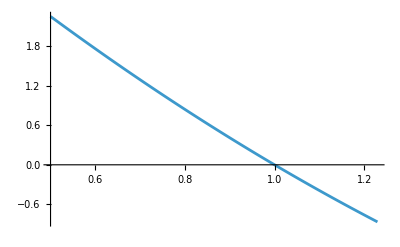

```mathematica
Plot[5-6 xx+xx^2,{xx,0.5,s0}]
```

Thus, we need to distibguish two cases.

If Δ̃≠0 (s^2≠1):

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}]//Simplify;
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}]//Simplify;
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}]//Simplify;
Dtilde=HeadOfTensor[2J[-a,-b,-c]-3ℐ[-a,-b]𝒦[-c]+𝒦[-a]𝒦[-b]𝒦[-c],{-a,-b,-c}]//Simplify;Dtilde[-a,-b,-c]
```

0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
-3 s^2 (-3+s^2) (-1+s^2)^2 |   |   |  
a | b | c

Thus, this solution is of type N[111].

If Δ̃=0 (s^2=1):

```mathematica
Ptilde=HeadOfTensor[𝒞tilde2[a,-b,-c,-d]ℐtilde[-e,-f]-𝒞tilde[a,-b,-c]Jtilde[-d,-e,-f]-1/3 Antisymmetrize[metric[a,-b]ℐtilde[-c,-d]ℐtilde[-e,-f],{-b,-c}],{a,-b,-c,-d,-e,-f}]/.{s->-1}//Simplify;
Ptilde[a,-b,-c,-d,-e,-f]===0
```

False

```mathematica
Dtilde[-a,-b,-c]/.{s->-1}//Simplify
```

0

```mathematica
Qtilde=HeadOfTensor[ℐ[-a,-b]-𝒦[-a]𝒦[-b],{-a,-b}]/.{s->-1};
Qtilde===Zero
```

True

Thus, this particular solution (with s^2=1) is of type N[2_01].

Let us obtain now their corresponding parameters:

```mathematica
𝓍=CTensor[{0,0,0,1},{chart}];
κ𝓍=𝒦[-a]𝓍[a];
ν𝓍=ℐ[-a,-b]𝓍[a]𝓍[b]//Simplify;
ξ𝓍=J[-a,-b,-c]𝓍[a]𝓍[b]𝓍[c]//Simplify;
α=ν𝓍/κ𝓍^2//Simplify
β=ξ𝓍/κ𝓍^3//Simplify
```

(-1-s^2+s^4)/(-2+s^2)

-(4+3 s^2-6 s^4+s^6)/(2 (-2+s^2)^3)

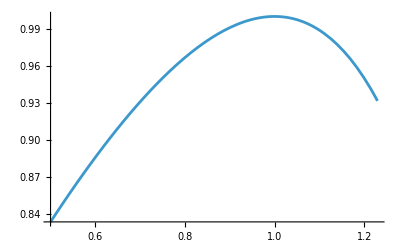

```mathematica
Plot[(-1-xx+xx^2)/(-2+xx),{xx,0.5,ssv}]
```

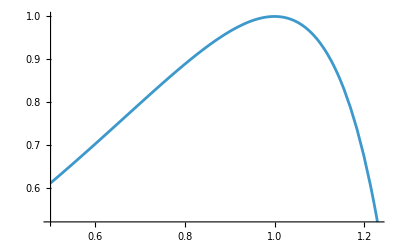

```mathematica
Plot[-(4+3 xx-6 xx^2+xx^3)/(2 (-2+xx)^3),{xx,0.5,ssv}]
```

For the particular case s^2=1:

```mathematica
{(-1-xx+xx^2)/(-2+xx)/.{xx->1},-(4+3 xx-6 xx^2+xx^3)/(2 (-2+xx)^3)/.{xx->1}}
```

{1,1}

### Class II (β^2=0)

```mathematica
UnsetCMetric[metric];
```

In this case, things go faster if we start with the variables undefined:

```mathematica
Clear[{A,B,F,𝒷,β}]
```

```mathematica
$Assumptions=𝒶∈Reals&&s∈Reals&&1+6 s^2-8 s^4+2 s^6==0;
```

```mathematica
betazero={s^6->(-1-6 s^2+8 s^4)/2};
```

```mathematica
metricMatrix=𝒶^2{{-1/4(𝒷-1/𝒷)^2 Exp[ z[]],-z[]/4(𝒷-1/𝒷)^2 Exp[ z[]],0,0},{-z[]/4(𝒷-1/𝒷)^2 Exp[ z[]],(1-z[]^2/4(𝒷-1/𝒷)^2)Exp[ z[]],0,0},{0,0,Exp[2F z[]],0},{0,0,0,1}}/.betazero//Simplify;
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
Solve[2 xx^3-8 xx^2+6 xx+1==0,xx];
s0=N[√(%[[2]][[1]][[2]])];
```

```mathematica
v=CTensor[{1/(√(-metric[{0,-chart},{0,-chart}])),0,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

and now, the connection tensor H:

```mathematica
𝒲=xAct`xIdeal`Private`weylConcomitant["WeylSelfDual"][metric,Verbose->False];
𝒲2=HeadOfTensor[1/2 𝒲[-a,-b,-i,-j]𝒲[i,j,-c,-d],{-a,-b,-c,-d}];
𝒲3=HeadOfTensor[1/2 𝒲2[-a,-b,-i,-j]𝒲[i,j,-c,-d],{-a,-b,-c,-d}]//Simplify;
aa=1/2 𝒲2[-a,-b,a,b]//Simplify;
bb=1/2 𝒲3[-a,-b,a,b]//Simplify;
CD=CovDOfMetric[metric];
𝒳=HeadOfTensor[CD[-a][𝒲[-b,-c,-d,-e]] 𝒲[d,e,c,-f]/2,{-a,-b,-f}];
𝒢2=xAct`xIdeal`Private`metricConcomitant["G2Form"][metric,Verbose->False]//Simplify;
𝒴=(3 aa 𝒲2+6 bb 𝒲+aa^2 𝒢2/2)/(aa^3-6 bb^2)//Simplify;
ℋ=HeadOfTensor[𝒳[-a,-b,-c] 𝒴[b,c,-d,-e]/√2,{-a,-d,-e}]//Simplify;
```

```mathematica
A=1/2(1-β);
B=1/2(1+β);
F=1-s^2;
𝒷=√2 s(3-s^2);
β=√(1+2 s^2(1-s^2)(3-s^2));
```

```mathematica
H=(ℋ+Dagger[ℋ])/Sqrt[2]//Simplify;H[-a,-b,-c]
```

0
0
0
● | 0
0
0
● | 0
0
0
0 | ●
●
0
0
0
0
0
● | 0
0
0
● | 0
0
0
0 | ●
●
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
ⅇ^(-2 (-1+s^2) z) (-1+s^2) a^2 | 0
0
-ⅇ^(-2 (-1+s^2) z) (-1+s^2) a^2
0
0
●
0
0 | ●
0
0
0 | 0
0
0
0 | 0
0
0
0 |   |   |  
a | b | c

With this, the dimension of the isometry group is obtained by using the corresponding xIdeal function:

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, we perform the classification algorithm:

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]/.{s->s0}//Simplify
```

0
0
0
-0.770319 |  
a

Thus, the algebra is non-unimodular.

```mathematica
nn=HeadOfTensor[1/2 epsilon[metric][a,c,d,e]𝒦[-c]𝒞[b,-d,-e],{a,b}]//Simplify
```

Zero

```mathematica
𝒞tilde=HeadOfTensor[𝒞[c,-a,-b]-1/3 2Antisymmetrize[metric[c,-a]𝒦[-b],{-a,-b}],{c,-a,-b}]//Simplify;(𝒞tilde[c,-a,-b]/.{s->s0}//Simplify)===0
```

False

```mathematica
𝒞tilde2=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde[c,-i,-d],{c,-a,-b,-d}]//Simplify;(𝒞tilde2[a,-b,-c,-d]/.{s->s0}//Simplify)===0
```

False

```mathematica
𝒞tilde3=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde2[c,-i,-d,-e],{c,-a,-b,-d,-e}]//Simplify;(𝒞tilde3[a,-b,-c,-d,-e]/.{s->s0}//Simplify)===0
```

False

```mathematica
ℐtilde=HeadOfTensor[𝒞tilde2[-a,a,-b,-c],{-b,-c}];
Jtilde=HeadOfTensor[𝒞tilde3[i,-i,-a,-b,-c],{-a,-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
νtilde=γ[a,b]ℐtilde[-a,-b]//Simplify;
μtilde=γ[a,c]γ[b,d]ℐtilde[-a,-b]ℐtilde[-c,-d]//Simplify;
σtilde=νtilde^2-μtilde//Simplify;
λ2tilde=γ[e,f]γ[a,c]γ[b,d]Jtilde[-a,-c,-e]Jtilde[-b,-d,-f]//Simplify;
Δtilde=νtilde^3-6λ2tilde//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[(Δtilde/.{s->s0}//Simplify)]
```

False

```mathematica
Δtilde/.{s->s0}//Simplify
```

0

As we have already seen in the previous section, Δ̃ vanishes for s=s_0.

```mathematica
Ptilde=HeadOfTensor[𝒞tilde2[a,-b,-c,-d]ℐtilde[-e,-f]-𝒞tilde[a,-b,-c]Jtilde[-d,-e,-f]-1/3 Antisymmetrize[metric[a,-b]ℐtilde[-c,-d]ℐtilde[-e,-f],{-b,-c}],{a,-b,-c,-d,-e,-f}]/.{s->-svn}//Simplify;
Ptilde[a,-b,-c,-d,-e,-f]===0
```

False

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}]//Simplify;
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}]//Simplify;
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}]//Simplify;
S=HeadOfTensor[2J[-a,-b,-c]-3ℐ[-a,-b]𝒦[-c]+𝒦[-a]𝒦[-b]𝒦[-c],{-a,-b,-c}]//Simplify;(S[-a,-b,-c]/.{s->svn}//Simplify)===0
```

False

Therefore, this solution is of type N[21]. Let us obtain its parameters:

```mathematica
α=(ℐ[-a,-c]𝒦[a]𝒦[c])/(𝒦[-b]𝒦[b])^2/.{s->svn}//Simplify
```

0.931517

```mathematica
β=(J[-a,-b,-c]𝒦[a]𝒦[b]𝒦[c])/(𝒦[-d]𝒦[d])^3/.{s->svn}//Simplify
```

0.520419

## Petrov solution

```mathematica
UnsetCMetric[metric];
```

We start by defining the metric and some constraints

```mathematica
DefConstantSymbol[kk,PrintAs->"k"];
$Assumptions=kk∈ Reals;
metricMatrix={{-E^x[] Cos[√3 x[]],0,0,-E^x[] Sin[√3 x[]]},{0,1,0,0},{0,0,E^(-2x[]),0},{-E^x[] Sin[√3 x[]],0,0,E^x[] Cos[√3 x[]]}}/kk^2;
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
v=CTensor[{E^(x[]/2)/(kk √Cos[√3 x[]]),0,0,0},{-chart}];v[a]v[-a]//Simplify
```

-1

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

and the dimension of the isometry group is obtained by using the corresponding xIdeal function:

```mathematica
H=ConnectionTensor[metric,Verbose->False];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, we perform the classification algorithm:

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}];𝒦[-a]
```

0

Thus, the algebra is unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}];L[e,-a,-b,-c,-d]
```

0

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];𝒞2[d,-a,-b,-c]===0
```

False

```mathematica
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;𝒞3[e,-a,-b,-c,-d]===0
```

False

So we need to study the sign of Δ:

```mathematica
ℐ=HeadOfTensor[𝒞2[a,-a,-b,-c],{-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
λ2=γ[e,f]γ[a,c]γ[b,d]J[-a,-c,-e]J[-b,-d,-f];
Δ=ν^3-6λ2//Simplify
```

-54 k^6

Since Δ<0 and

```mathematica
J[-a,-b,-c]===0
```

False

this solution is of type U[z z̄ 1].

## Petrov solution step-by-step

```mathematica
UnsetCMetric[metric];
```

We start by defining the metric and some constraints

```mathematica
DefConstantSymbol[kk,PrintAs->"k"];
$Assumptions=kk∈ Reals;
metricMatrix={{-E^x[] Cos[√3 x[]],0,0,-E^x[] Sin[√3 x[]]},{0,1,0,0},{0,0,E^(-2x[]),0},{-E^x[] Sin[√3 x[]],0,0,E^x[] Cos[√3 x[]]}}/kk^2;
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

Next, we determine its Petrov-Bel Type as explained in [30]: we start by defining an observer and obtaining some metric concomitants

```mathematica
v=CTensor[{E^(x[]/2)/(kk √Cos[√3 x[]]),0,0,0},{-chart}];
CD=CovDOfMetric[metric];
WeylCD=Weyl[CD];
Epsilonmetric=epsilon[metric];
WeylDual=HeadOfTensor[1/2 Epsilonmetric[-c,-d,-e,-f] WeylCD[e,f,-a,-b],{-c,-d,-a,-b}]//Simplify;
WeylSelfDual=1/2 (WeylCD-I*WeylDual)//Simplify;
Q=HeadOfTensor[2 v[a] v[c] WeylSelfDual[-a,-b,-c,-d],{-b,-d}]//Simplify;
gamma=HeadOfTensor[metric[-a,-b]-v[-a] v[-b],{-a,-b}]//Simplify;
Q2=HeadOfTensor[Q[-a,-b] Q[b,-c],{-a,-c}]//Simplify;
aa=Q2[a,-a]//Simplify;
Q3=HeadOfTensor[Q2[-a,-b] Q[b,-c],{-a,-c}]//Simplify;
bb=Q3[a,-a]//Simplify;
```

Then, we follow the IDEAL algorithm determining the Petrov-Bel Type:

```mathematica
Which[
	Q===Zero,
		"Type O",
	Q2===Zero,
		"Type N",
	Q3===Zero,
		"Type III",
	Simplify[(aa^2/3) gamma-aa Q2-bb Q]===Zero,
		"Type D",
	Simplify[6 bb^2-aa^3]===0,
		"Type II",
	True,
		"Type I"]
```

Type I

With this, the dimension of the isometry group is obtained as explained in [8]. First we obtain the connection tensor which, for the case of a Petrov-Bel Type I metric, can be done as follows:

```mathematica
WeylSelfDual2=HeadOfTensor[1/2 WeylSelfDual[-a,-b,e,f] WeylSelfDual[-e,-f,-c,-d],{-a,-b,-c,-d}]//Simplify;
G2form=HeadOfTensor[1/2 (-I Epsilonmetric[-a,-b,-c,-d]+metric[-a,-c] metric[-b,-d]-metric[-a,-d] metric[-b,-c]),{-a,-b,-c,-d}];
𝒳=HeadOfTensor[CD[-a][WeylSelfDual[-b,-c,-d,-e]]WeylSelfDual[d,e,c,-f]/2,{-a,-b,-f}];
𝒴=(3 aa WeylSelfDual2-6 bb WeylSelfDual+aa^2 G2form/2)/(aa^3-6 bb^2)//Simplify;
selfdualH=HeadOfTensor[𝒳[-a,-b,-c] 𝒴[b,c,-d,-e]/√2,{-a,-d,-e}]//Simplify;
H=(selfdualH+Dagger[selfdualH])/√2//Simplify;
```

and once we have it, we perform the algorithm to determine the dimension of the isometry group (summarised for the case of a G_4 in Theorem 1):

```mathematica
C1=CD[-a][H[-b,-c,-d]]+H[-a,-b,i] H[-i,-c,-d]+H[-a,-c,i] H[-b,-i,-d]+H[-a,-d,i] H[-b,-c,-i]//Simplify
```

0

So this metric indeed admits a G_4.

Now, we perform the classification algorithm of Figure 1:

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}];𝒦[-a]
```

0

Thus, the algebra is unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}];L[e,-a,-b,-c,-d]===0
```

True

```mathematica
𝒞===0
```

False

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];𝒞2[d,-a,-b,-c]===0
```

False

```mathematica
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;𝒞3[e,-a,-b,-c,-d]===0
```

False

So we need to study the sign of Δ:

```mathematica
ℐ=HeadOfTensor[𝒞2[a,-a,-b,-c],{-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
λ2=γ[e,f]γ[a,c]γ[b,d]J[-a,-c,-e]J[-b,-d,-f];
Δ=ν^3-6λ2//Simplify
```

-54 k^6

Since Δ<0 and

```mathematica
J[-a,-b,-c]===0
```

False

this solution is of type U[z z̄ 1].

## Other solutions 1

We start by defining the metric (44) and some constraints

```mathematica
UnsetCMetric[metric];
```

```mathematica
$Assumptions=𝒶∈Reals;
```

```mathematica
metricMatrix={{-1,0,0,2y[]},{0,𝒶^2/x[]^2,0,0},{0,0,𝒶^2/x[]^2,0},{2y[],0,0,x[]^2-4 y[]^2}};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{1/(√(-metric[{0,-chart},{0,-chart}])),0,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

and the dimension of the isometry group is obtained by using the corresponding xIdeal function:

```mathematica
H=ConnectionTensor[metric,Verbose->False];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, let us perform the classification algorithm.

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]
```

0

Thus, the algebra is unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}]//Simplify;L[e,-a,-b,-c,-d]===0
```

False

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
ℐ=HeadOfTensor[𝒞2[a,-a,-b,-c],{-b,-c}];
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
J[-a,-b,-c]===0
```

True

```mathematica
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[ν]
```

True

This solution is of type U(1,+1).

## Other solutions 2

We start by defining the metric (45) and some constraints

```mathematica
UnsetCMetric[metric];
```

```mathematica
DefConstantSymbol[Λ];
```

```mathematica
$Assumptions=Λ∈Reals&&Λ>0&&z[]∈Reals;
```

```mathematica
metricMatrix={{0,E^(-2z[]),0,0},{E^(-2z[]),E^(4z[]),2 E^z[],0},{0,2 E^z[],2 E^(-2z[]),0},{0,0,0,3/Λ}};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{(1+E^(4z[]))/2 E^(2z[]),-1,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type III

and the dimension of the isometry group is obtained by using the corresponding xIdeal function. For that we need an arbitrary bivector:

```mathematica
X=CTensor[{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{1,0,0,0}},{-chart,-chart}];𝒲2=xAct`xIdeal`Private`weylConcomitant["WeylSelfDual2"][metric,Verbose->False];𝒲2[-a,-b,-c,-d]X[c,d]
```

0 | 0 | 0 | 0
0 | 0 | (ⅈ ⅇ^(5 z) Λ^(5/2))/(√6) | -1/2 ⅇ^(6 z) Λ^2
0 | -(ⅈ ⅇ^(5 z) Λ^(5/2))/(√6) | 0 | 0
0 | 1/2 ⅇ^(6 z) Λ^2 | 0 | 0 |   |  
a | b

```mathematica
H=ConnectionTensor[metric,Verbose->False,"Bivector"->X];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, let us perform the classification algorithm.

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]
```

0
0
0
3 |  
a

Thus, the algebra is non-unimodular.

```mathematica
nn=HeadOfTensor[1/2 epsilon[metric][a,c,d,e]𝒦[-c]𝒞[b,-d,-e],{a,b}]//Simplify
```

Zero

```mathematica
𝒞tilde=HeadOfTensor[𝒞[c,-a,-b]-1/3 2Antisymmetrize[metric[c,-a]𝒦[-b],{-a,-b}],{c,-a,-b}]//Simplify;𝒞tilde[c,-a,-b]===0
```

False

```mathematica
𝒞tilde2=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde[c,-i,-d],{c,-a,-b,-d}]//Simplify;𝒞tilde2[a,-b,-c,-d]===0
```

False

```mathematica
𝒞tilde3=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde2[c,-i,-d,-e],{c,-a,-b,-d,-e}]//Simplify;𝒞tilde3[a,-b,-c,-d,-e]===0
```

False

```mathematica
ℐtilde=HeadOfTensor[𝒞tilde2[-a,a,-b,-c],{-b,-c}];
Jtilde=HeadOfTensor[𝒞tilde3[i,-i,-a,-b,-c],{-a,-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
νtilde=γ[a,b]ℐtilde[-a,-b]//Simplify;
μtilde=γ[a,c]γ[b,d]ℐtilde[-a,-b]ℐtilde[-c,-d]//Simplify;
σtilde=νtilde^2-μtilde//Simplify;
λ2tilde=γ[e,f]γ[a,c]γ[b,d]Jtilde[-a,-c,-e]Jtilde[-b,-d,-f]//Simplify;
Δtilde=νtilde^3-6λ2tilde//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[Δtilde]
```

True

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}]//Simplify;
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}]//Simplify;
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}]//Simplify;
Dtilde=HeadOfTensor[2J[-a,-b,-c]-3ℐ[-a,-b]𝒦[-c]+𝒦[-a]𝒦[-b]𝒦[-c],{-a,-b,-c}]//Simplify;Dtilde[-a,-b,-c]
```

0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
-48 |   |   |  
a | b | c

This solution is of type N[111]. Let us obtain now its parameters:

```mathematica
xx=CTensor[{0,0,0,1},{chart}];
κx=𝒦[-a]xx[a]
```

3

```mathematica
νx=ℐ[-a,-b]xx[a]xx[b]//Simplify
```

21

```mathematica
ξx=J[-a,-b,-c]xx[a]xx[b]xx[c]//Simplify
```

57

```mathematica
α=νx/κx^2//Simplify
```

7/3

```mathematica
β=ξx/κx^3//Simplify
```

19/9